# Лабораторна робота №1

## Завдання №1 (Варіант 6)

Маємо рівняння .

```mathematica
f[x_, y_] := y^2 + y + x
```

## 1)

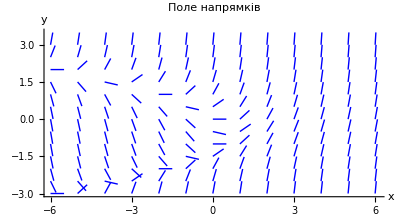

```mathematica
Graphics[{Blue,Arrowheads[0],Table[Module[{f=y^2+y+x,dt=0.5},With[{dir={1,f}/Sqrt[1+f^2]},Arrow[{{x,y},{x,y}+dt*dir}]]],{x,-6,6,1},{y,-3,3,0.5}]},Axes->True,AxesLabel->{"x","y"}, PlotLabel -> Style["Поле напрямків", 14, Bold, Blue]]
```

## 2)

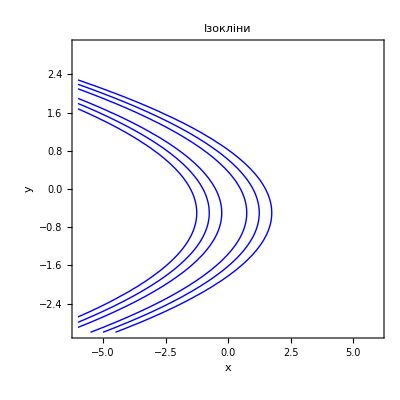

```mathematica
ContourPlot[y^2+y+x,{x,-6,6},{y,-3,3},Contours->{-1/2,1/2,1,-1,-3/2, 3/2},ContourStyle->{Blue},ContourShading->None,PlotLabel->Style["Ізокліни",14, Bold, Orange],AxesLabel->{"x","y"}]
```

## 3)

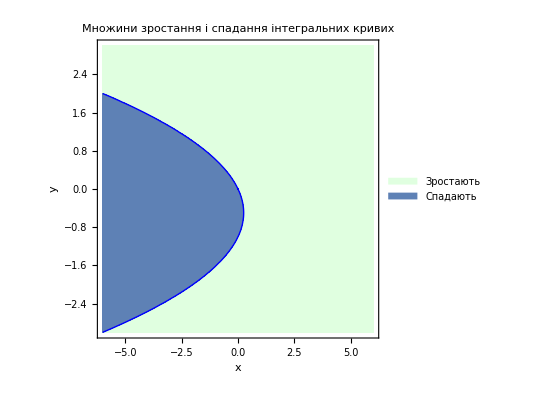

```mathematica
Show[RegionPlot[f[x,y]>0,{x,-6,6},{y,-3,3},PlotStyle->LightGreen,BoundaryStyle->None,PlotLegends->Placed[{"Зростають"},{0.8,0.8}]],RegionPlot[f[x,y]<0,{x,-6,6},{y,-3,3},PlotStyle->LightCoral,BoundaryStyle->None,PlotLegends->Placed[{"Спадають"},{0.8,0.7}]],ContourPlot[f[x,y],{x,-6,6},{y,-3,3},Contours->{0},ContourStyle->{Thick,Blue},ContourShading->None,Frame->False,Axes->False],Axes->True,AxesLabel->{"x","y"},PlotLabel->Style["Множини зростання і спадання інтегральних кривих",14,Bold]]
```

## 4)

Аби знайти точки максимуму, необхідно знайти другу похідну функції :  .  Маємо умови: .   — хиба, отже стаціонарні можуть бути лише точками мінімуму.

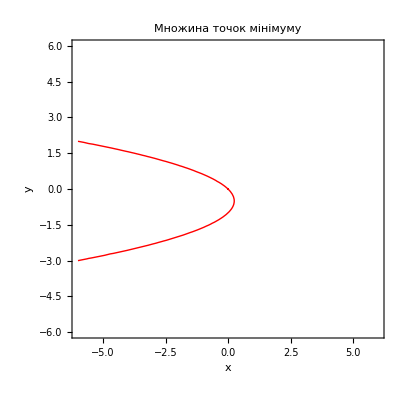

```mathematica
Show[ContourPlot[f[x,y],{x,-6,6},{y,-6,6},Contours->{0},ContourStyle->{Thick,Red},ContourShading->None,AxesLabel->{"x","y"},PlotLabel->Style["Множина точок мінімуму",14,Bold, Red]],RegionPlot[f_x[x,y]<0,{x,-6,6},{y,-6,6},PlotStyle->LightRed,BoundaryStyle->None]]
```

## 5, 6)

Аби знайти, де інтегральні криві опуклі вгору, опуклі вниз, та точки перегину, треба порівняти другу похідну з нулем.  . 
.

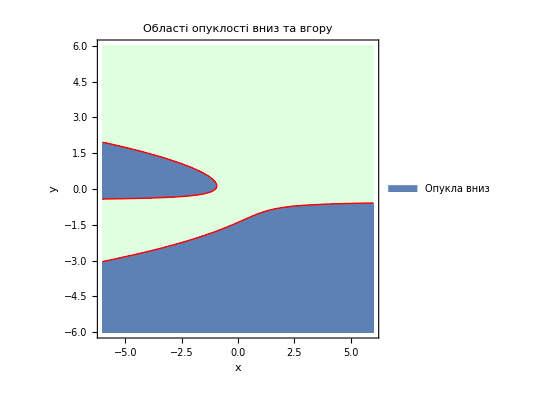

```mathematica
secondDeriv[x_,y_]:=(2 y+1) (y^2+y+x)+1

inflectionPlot=ContourPlot[secondDeriv[x,y]==0,{x,-6,6},{y,-6,6},ContourStyle->{Thick,Red},ContourShading->None,Epilog->{Text[Style["Точки перегину",14,Bold,Red],{-4,2}]},AxesLabel->{"x","y"},PlotLegends->Placed[{"Точки перегину"},{0.8,0.8}]];

(*Regions of convexity*)
regionUp=RegionPlot[secondDeriv[x,y]>0,{x,-6,6},{y,-6,6},PlotStyle->LightGreen,BoundaryStyle->None,AspectRatio->1,PlotLegends->Placed[{"Опукла вгору"},{0.8,0.8}]];

regionDown=RegionPlot[secondDeriv[x,y]<0,{x,-6,6},{y,-6,6},PlotStyle->LightCoral,BoundaryStyle->None,AspectRatio->1,PlotLegends->Placed[{"Опукла вниз"},{0.8,0.7}]];

Show[regionUp,regionDown,inflectionPlot,Axes->True,AxesLabel->{"x","y"},PlotLabel->Style["Області опуклості вниз та вгору",14,Bold]]
```

## 7)

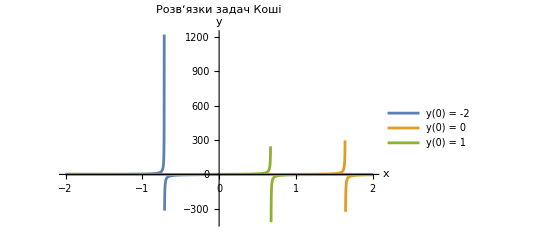

```mathematica
sol1=f[x]/. DSolve[{f'[x]==f[x]^2+f[x]+x,f[0]==-2},f[x],x][[1]];
sol2=f[x]/. DSolve[{f'[x]==f[x]^2+f[x]+x,f[0]==0},f[x],x][[1]];
sol3=f[x]/. DSolve[{f'[x]==f[x]^2+f[x]+x,f[0]==1},f[x],x][[1]];

Plot[{sol1,sol2,sol3},{x,-2,2},PlotLegends->{"y(0) = -2","y(0) = 0","y(0) = 1"},AxesLabel->{"x","y"},PlotRange->All, PlotLabel->Style["Розв‘язки задач Коші",14,Bold, Black]]
```

## Завдання №2 (Варіант 6)

Маємо рівняння: ^

```mathematica
g[y_] := 2y - y^2 + 3
```

## 1)

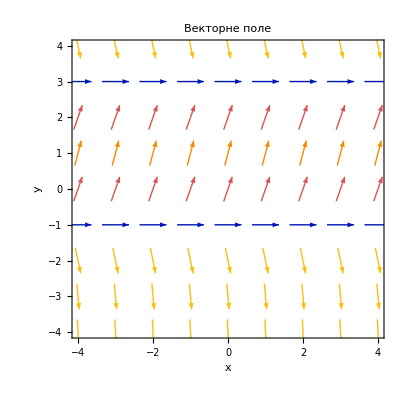

```mathematica
VectorPlot[{1,2 y-y^2+3},{x,-4,4},{y,-4,4},VectorPoints->Flatten[Table[{x,y},{x,-4,4},{y,-4,4}],1],VectorStyle->{Black,Arrowheads[0.02]},AxesLabel->{"x","y"}, PlotLabel-> Style["Векторне поле", 14, Bold, Black]]
```

## 2)

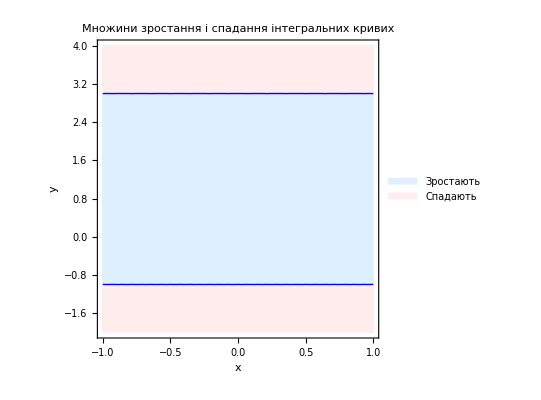

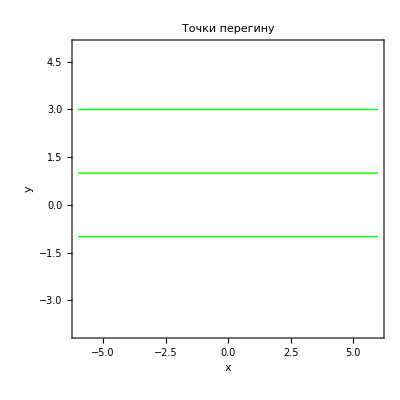

```mathematica
Show[RegionPlot[g[y]>0,{x,-1,1},{y,-2,4},PlotStyle->LightBlue,BoundaryStyle->None,PlotLegends->Placed[{"Зростають"},{0.8,0.8}]],RegionPlot[g[y]<0,{x,-1,1},{y,-2,4},PlotStyle->LightPink,BoundaryStyle->None,PlotLegends->Placed[{"Спадають"},{0.8,0.7}]],ContourPlot[g[y],{x,-1,1},{y,-2,4},Contours->{0},ContourStyle->{Blue},ContourShading->None,Frame->False,Axes->False],Axes->True,AxesLabel->{"x","y"},PlotLabel->Style["Множини зростання і спадання інтегральних кривих",14,Bold]]

ContourPlot[(2-2 y) (2 y-y^2+3)==0,{x,-6,6},{y,-4,5},ContourStyle->{Thick,Green},ContourShading->None,AxesLabel->{"x","y"},PlotLabel->Style["Точки перегину",14,Bold]]
```

## 3)

| ^4




Тепер розв‘яжемо задачу Коші 
A) 
B) 

Після підстановки ми знайдемо інтервали:
Для  є асимптота . 
Для  є асимптота . 
Для .

## 4)

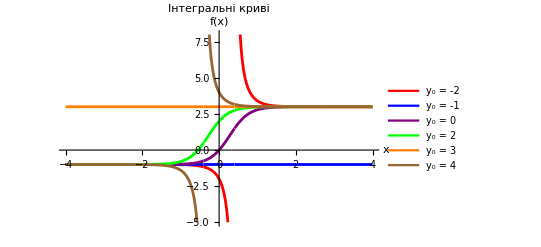

```mathematica
ClearAll[f,x,y0];
solution=DSolve[{f'[x]==2 f[x]-f[x]^2+3,f[0]==y0},f[x],x]
fSol[x_,y0_]=f[x]/. First[solution]
{y1,y2}={-1,3};
initialConditions={-2,-1,0,2,3,4};
Plot[Evaluate@Table[fSol[x,y0],{y0,initialConditions}],{x,-4,4},PlotRange->{-5,8},PlotStyle->{Red,Blue,Purple,Green,Orange,Brown},PlotLegends->Placed[LineLegend[{Red,Blue,Purple,Green,Orange,Brown},"y₀ = "<>ToString[#]&/@initialConditions],Above],AxesLabel->{"x","f(x)"},PlotLabel->Style["Інтегральні криві",Bold,14]]
```

## 5)

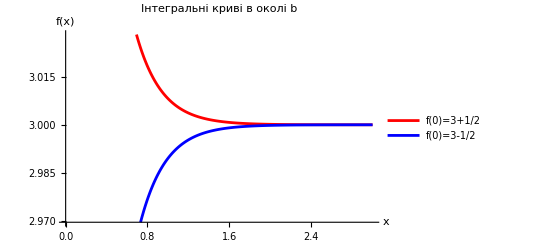

{x→1.73087}

```mathematica
ClearAll[f,x,b];

eq=f'[x]==2 f[x]-f[x]^2+3;

b=3; (*інтервал J від 3 до +нескінченності*)

solUp=DSolve[{eq,f[0]==b+1/2},f[x],x];
solDown=DSolve[{eq,f[0]==b-1/2},f[x],x];

fUp[x_]=f[x]/. solUp[[1]];
fDown[x_]=f[x]/. solDown[[1]];

Plot[{fUp[x],fDown[x]},{x,0,3},PlotStyle->{Red,Blue},AxesLabel->{"x","f(x)"},PlotLegends->Placed[{"f(0)=3+1/2","f(0)=3-1/2"},Above],PlotLabel->Style["Інтегральні криві в околі b",14,Bold]]

FindRoot[Abs[fUp[x]-fDown[x]]==10^-3,{x,1,0,3}]
```